## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSFittingPackage`"];
Get["MASSFittingPackage`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="ADK1";
KeqEquilibrator=1.97;

(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/MASS_fitting_package/";

dataFolder = "ADK1_fit_dKd";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, dataFolder];
```

Working dir:/home/mrama/Dropbox/MASS_fitting_package/examples/

## Import Data From Database

```mathematica
enzymeDataPath = pathData <> "kinetic_data.xls";
bufferInfoDataPath = pathData <> "buffer_info.xls";
ionChargeDataPath = pathData <> "ion_charge.xls";

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
rxn
mechanism
"Structure "<>ToString@structure
"Active sites "<>ToString@nActiveSites

(*Print Available Kinetic Data*)
{{"Km Values:","(kmList)"},
{"Substrate","Km_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kmList//TableForm
{{"S0.5 Values:","(s05List)"},
{"Substrate","S0.5_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~s05List//TableForm
{{"kcat Values:","(kcatList)"},
{"Metabolite(s)","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kcatList//TableForm
{{"Inhibition Values:","(inhibitionList)"},
{"Parameter_Type","Inhibitor","Value","Inhibition Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~inhibitionList//TableForm
{{"Activation Values:","(activationList)"},
{"Parameter_Type","Activator","Value","Activation Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~activationList//TableForm
{{"Other Parameters:","(otherParms)"},
{"Parameter_Type","Metabolite","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~otherParmsList//TableForm
```

(amp^c+atp^c⇌2 adp^c)^ADK1

Random Bi Bi,[adp, adp, atp || amp, adp || atp]

Structure 1.

Active sites 1.

Km Values: | (kmList) |  |  |  |  |  | 
Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
adp | 0.000105 |  | M | 7.4 | 40. | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
atp | 0.000046 | amp | 0.001 | M | 7.4 | 40. | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
amp | 0.000044 | atp | 0.001 | M | 7.4 | 40. | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

S0.5 Values: | (s05List) |  |  |  |  |  | 
Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values: | (kcatList) |  |  |  |  | 
Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
adp | Null | 319. | 1/s | 7.4 | 40. | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
amp | Null
atp | Null | 1296. | 1/s | 7.4 | 40. | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

Inhibition Values: | (inhibitionList) |  |  |  |  |  |  | 
Parameter_Type | Inhibitor | Value | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values: | (activationList) |  |  |  |  |  |  | 
Parameter_Type | Activator | Value | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters: | (otherParms) |  |  |  |  |  | 
Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct Enzyme Module

```mathematica
catalyticBranch={"E_ADK1[c] + amp[c] <=> E_ADK1[c]&amp",
				"E_ADK1[c] + atp[c] <=> E_ADK1[c]&atp",
				"E_ADK1[c]&atp + amp[c] <=> E_ADK1[c]&atp&amp",
				"E_ADK1[c]&amp + atp[c] <=> E_ADK1[c]&atp&amp",
				"E_ADK1[c]&atp&amp <=> E_ADK1[c]&adp&adp",
				"E_ADK1[c]&adp&adp <=> E_ADK1[c]&adp + adp[c]",
				"E_ADK1[c]&adp <=> E_ADK1[c] + adp[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
competitiveRxns={{}};
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions, competitiveRxns];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];
```

default absoluteFluxEqnRelRateFor

default absoluteFluxEqnRelRateRev

#### ADK1 Specific Work-Around for Double Substrate Binding Effects

```mathematica
symbolicKmReverse=Solve[((absoluteFlux[[2]]/.eqRateConstSub)/.forwardZeroSub/.eqRateConstSub)== Limit[((absoluteFlux[[2]]/.eqRateConstSub)/.forwardZeroSub/.eqRateConstSub),adp^c-> ∞]/2,adp^c];
relativeRateReverse[[1]]=Simplify[symbolicKmReverse[[1,1,2]](*/.haldaneSub/.eqRateConstSub*)];
```

```mathematica
(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={7.4, 40};

kmFittingData= simulateKmData[rxn, metsFull, metsSub, metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath, inputPath, fileList, KeqEquilibrator];

kcatFittingData=simulateKcatData[rxn, metsFull, metsSub, metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  inputPath, fileList, KeqEquilibrator];

haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
KeqRatio=haldane[[2]]/.eqRateConstSub;

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[KeqRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];
```

#### ADK1 Specific Work-Around for Double Substrate Binding Effects

```mathematica
(*Set All Substrates to Zero*)
kmAdpPt=Join[
{1.97,0,0},kmFittingData[[1,4;;-2]]];
(*Set Target Value to Km(ADP) Value*)
kmAdpPt=AppendTo[kmAdpPt,kmList[[1,2]]];
(*Create a Replacement Rule List. Km(ADP) values are at the beginning of the list*)
repDataPt=Table[
dataPt->kmAdpPt,
{dataPt,1,nonKmParamWeight}];
(*Actual Replacement*)
kmFittingData=ReplacePart[kmFittingData,repDataPt]
```

{{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0,0,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt,0.000105},{1.97,0,0.001,4.6×10^-6,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.0909091},{1.97,0,0.001,7.29051×10^-6,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.136807},{1.97,0,0.001,0.0000115547,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.20076},{1.97,0,0.001,0.0000183129,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.284747},{1.97,0,0.001,0.000029024,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.386863},{1.97,0,0.001,0.000046,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.5},{1.97,0,0.001,0.0000729051,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.613137},{1.97,0,0.001,0.000115547,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.715253},{1.97,0,0.001,0.000183129,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.79924},{1.97,0,0.001,0.00029024,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.863193},{1.97,0,0.001,0.00046,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt,0.909091},{1.97,0,4.4×10^-6,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.0909091},{1.97,0,6.97353×10^-6,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.136807},{1.97,0,0.0000110523,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.20076},{1.97,0,0.0000175167,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.284747},{1.97,0,0.0000277621,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.386863},{1.97,0,0.000044,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.5},{1.97,0,0.0000697353,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.613137},{1.97,0,0.000110523,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.715253},{1.97,0,0.000175167,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.79924},{1.97,0,0.000277621,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.863193},{1.97,0,0.00044,0.001,1,7.4,40.,/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt,0.909091}}

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData,KeqFittingData}, 1];

dataPath =inputPath<>rxnName<>".dat";

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_ADK1	adp[c]	amp[c]	atp[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateRev_adp.txt	0.00010499999999999999
1.97	0	0.001	4.6000000000000025e-6	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.09090909090909097
1.97	0	0.001	7.290508685321129e-6	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.1368068886032101
1.97	0	0.001	0.000011554677584944084	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.20076000891310194
1.97	0	0.001	0.00001831292984546087	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.28474724895080133
1.97	0	0.001	0.000029024037846088895	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.386863179846857
1.97	0	0.001	0.00004600000000000003	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.5000000000000001
1.97	0	0.001	0.00007290508685321129	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.6131368201531432
1.97	0	0.001	0.00011554677584944084	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.7152527510491989
1.97	0	0.001	0.00018312929845460887	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.7992399910868985
1.97	0	0.001	0.0002902403784608889	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.8631931113967901
1.97	0	0.001	0.00046000000000000023	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_atp.txt	0.9090909090909091
1.97	0	4.399999999999995e-6	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.09090909090909081
1.97	0	6.973530046828895e-6	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.13680688860320994
1.97	0	0.00001105230029864215	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.20076000891310172
1.97	0	0.000017516715504353882	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.28474724895080145
1.97	0	0.000027762123157128463	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.3868631798468566
1.97	0	0.00004399999999999995	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.4999999999999998
1.97	0	0.00006973530046828894	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.6131368201531429
1.97	0	0.0001105230029864215	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.7152527510491986
1.97	0	0.00017516715504353863	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.7992399910868981
1.97	0	0.00027762123157128464	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.8631931113967899
1.97	0	0.00043999999999999953	0.001	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/relRateFor_amp.txt	0.9090909090909091
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0.01	0	0	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateRev.txt	319.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0.01	0.01	1	7.4	40.	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/absRateFor.txt	1296.
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97
1.97	0	0	0	1	7.4	40	/home/mrama/Dropbox/MASS_fitting_package/examples/ADK1_fit_dKd/input/haldaneRatio.txt	1.97

## Configure the Particle Swarm Optimization

```mathematica
numTrials=5;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound];
```

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound];
```

### Make the shell script to run pso and lma fitting methods

```mathematica
runFitScriptPath= pathMASSFittingPackage <> "python_code/src/run_fit_rel.py"
shRunFit=createCombinedFitShellScript[runFitScriptPath, psoParameterPath, lmaParameterPath, psoTrialSummaryFileName, psoResultsFileName, lmaResultsFileName, numTrials, dataPath];

shRunFitPath=inputPath<>"runFit.sh";
Export[shRunFitPath,shRunFit,"Table"];

(*Make the Shell Script Executable*)
mkShRunFitExec="chmod u+x "<> shRunFitPath;
mkShRunFitExecCmd="!"<>mkShRunFitExec<>" 2>&1";
Import[mkShRunFitExecCmd,"Text"];
```

/home/mrama/Dropbox/MASS_fitting_package/python_code/src/run_fit_rel.py

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothCmd="cd "<>inputPath<>" && ./"<>"runFit.sh";
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

best_fit: 1.08069977906
best_fit: 29.9437682048
best_fit: 1.0693437154
best_fit: 30.4118198968
best_fit: 1.09966604748

#### Run the PSO Algorithm Independently

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/ADK1/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /home/mrama/Dropbox/Kinetics/Scripts/lma_ver0.10.1.py /home/mrama/Dropbox/Kinetics/Enzymes_new/ADK1/Parameter_Fitting/Development/lmaParameters.txt /home/mrama/Dropbox/Kinetics/Enzymes_new/ADK1/Parameter_Fitting/Development/psoResults.txt /home/mrama/Dropbox/Kinetics/Enzymes_new/ADK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

### Run Fitting on A Remote Batch System

#### Section Inputs

Note: all of the inputs in this section need to be strings

```mathematica
templateFile="/media/users/jdebree/ProjectFiles/Scripts/template.sh";(*Template file for running remote batch system jobs*)
sshProfileName="carver"; (*Need to use ssh-keygen and ssh-agent(See "Configuring an SSH Profile" documentation)*)
batchScriptlocation="/media/users/jdebree/ProjectFiles/Scripts/";
batchScriptName="run_pso_s_nodes.sh";
remotePythonDir="/global/homes/d/dczielin/ProjectFiles/Scripts/pso_short_ver0.09.1.py";
remoteLmaDir="/global/homes/d/dczielin/ProjectFiles/Scripts/lma_ver0.10.1.py";
jobQueue="debug";
jobName="RemoteTest";
repoName="m1497";
maxWallTime="00:30:00";
numNodes="1";
numCoresPerNode="8";
numTrialsPerNode="8";
```

#### Put the Run Dependencies on the Remote System

The Mathematica Shell interface does not like ssh logins so a shell script is necessary for remote interfacing

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
mkDirRemoteSysCmd={"ssh "<>sshProfileName<>" mkdir -p "<>paramWorkingDir<>"Parameter_Fitting"};
dataToRemoteSysCmd={"cd "<>outputPath<>";cd ..;tar cz " <>outputDir<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramWorkingDir<>"Parameter_Fitting"};
shDataToRemoteSys={shebangLine,{(*Spacer*)},mkDirRemoteSysCmd,dataToRemoteSysCmd};
shDataToRemoteSysName="dataToRemoteSys.sh";
shDataToRemoteSysPath="~/"<>shDataToRemoteSysName;
Export[shDataToRemoteSysPath,shDataToRemoteSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToRemoteSysExec="chmod u+x "<> shDataToRemoteSysPath;
mkShDataToRemoteSysExecCmd="!"<>mkShDataToRemoteSysExec<>" 2>&1";
Import[mkShDataToRemoteSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToRemoteSys="./"<>shDataToRemoteSysName;
runShDataToRemoteSysCmd="!"<>runShDataToRemoteSys<>" 2>&1";
Import[runShDataToRemoteSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToRemoteSys="rm "<>shDataToRemoteSysPath;
delShDataToRemoteSysCmd="!"<>delShDataToRemoteSys<>" 2>&1";
Import[delShDataToRemoteSysCmd,"Text"];
```

#### Run a Batch Job on the Remote System (Note: This was written for the Carver System at NERSC) WARNING: This Cell Executes A Job Based on the Inputs Above

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
shSubmitJob={shebangLine,{(*Spacer*)},{"# Variable Inputs"}};

setPythonDir={"python_Dir=\""<>remotePythonDir<>"\""};
setQueue={"job_queue="<>jobQueue};
shSubmitJob=Append[shSubmitJob,setQueue];
setJobName={"job_name="<>jobName};
shSubmitJob=Append[shSubmitJob,setJobName];
setRepoName={"repo="<>repoName};
shSubmitJob=Append[shSubmitJob,setRepoName];
setMaxWallTime={"maxWallTime="<>maxWallTime};
shSubmitJob=Append[shSubmitJob,setMaxWallTime];
setNumNodes={"num_nodes="<>numNodes};
shSubmitJob=Append[shSubmitJob,setNumNodes];
setNumCoresPerNode={"num_cores_per_node="<>numCoresPerNode};
shSubmitJob=Append[shSubmitJob,setNumCoresPerNode];
setNumTrialsPerNode={"num_trials_per_node="<>numTrialsPerNode};
shSubmitJob=Append[shSubmitJob,setNumTrialsPerNode];
shSubmitJob=Append[shSubmitJob,setPythonDir];
setRunDir={"run_Dir=\""<>paramOutputPath<>"\""};
shSubmitJob=Append[shSubmitJob,setRunDir];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Make the Batch Script Using the Template"}];
mkBatchScript={"> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,mkBatchScript];
pbsJobQueue={"pbsQ=\"#PBS -q "<>jobQueue<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobQueue];
setPbsJobQueue={"echo $pbsQ >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobQueue];
pbsJobName={"pbsN=\"#PBS -N "<>jobName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobName];
setPbsJobName={"echo $pbsN >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobName];
pbsRepo={"pbsA=\"#PBS -A "<>repoName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsRepo];
setPbsRepo={"echo $pbsA >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsRepo];
pbsNodeConfig={"pbsL=\"#PBS -l nodes="<>numNodes<>":ppn="<>numCoresPerNode<>",walltime="<>maxWallTime<>"\""};
shSubmitJob=Append[shSubmitJob,pbsNodeConfig];
setPbsNodeConfig={"echo $pbsL >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsNodeConfig];
addTemplateFile={"cat "<>templateFile<>" >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,addTemplateFile];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Push Batch Script to the Remote System"}];
dataToRemoteSysCmd={"tar cz " <>batchScriptName<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramOutputPath};
shSubmitJob=Append[shSubmitJob,dataToRemoteSysCmd];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Run the Job on the Remote System"}];
jobSubmissionArguments="n_nodes="<>numNodes<>",n_cores_p_node="<>numCoresPerNode<>",n_trials="<>numTrialsPerNode<>",pythonDir=\""<>remotePythonDir<>"\",runDir=\""<>paramOutputPath<>"\",lmaDir=\""<>remoteLmaDir<>"\"";
actuallySubmitJobCmd={submitJobCmd="ssh "<> sshProfileName<>" \"cd "<>paramOutputPath<>" && source ~/.bash_profile; qsub -v "<>jobSubmissionArguments<>" run_pso_s_nodes.sh\""};
shSubmitJob=Append[shSubmitJob,actuallySubmitJobCmd];

shSubmitJobName="submitJob.sh";
shSubmitJobPath="~/"<>shSubmitJobName;
Export[shSubmitJobPath,shSubmitJob,"Table"];

(*Make the Shell Script Executable*)
mkShSubmitJobExec="chmod u+x "<> shSubmitJobPath;
mkShSubmitJobExecCmd="!"<>mkShSubmitJobExec<>" 2>&1";
Import[mkShSubmitJobExecCmd,"Text"];

(*Run the Shell Script*)
runShSubmitJob="./"<>shSubmitJobName;
runShSubmitJobCmd="!"<>runShSubmitJob<>" 2>&1";
Import[runShSubmitJobCmd,"Text"];
```

```mathematica
(*Review Nersc Interfacing Batch Script (Optional)*)
FilePrint[shSubmitJobPath]
```

#### Pull Files from the Remote System (This might take some time for large runs)

```mathematica
(*Manually Enter the Run Folder Name (Optional)*)
(*outputDir="Run_1_7_15.54";*)
```

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
dataToLocalSysCmd={dataToLocalSysCmd="ssh "<> sshProfileName<>" \"cd "<>paramWorkingDir<>"Parameter_Fitting/ && tar cz "<>outputDir<>"\"|tar zxv -C "<>workingDir<>"Parameter_Fitting/"}; 
shDataToLocalSys={shebangLine,{(*Spacer*)},dataToLocalSysCmd};
shDataToLocalSysName="dataToLocalSys.sh";
shDataToLocalSysPath="~/"<>shDataToLocalSysName;
Export[shDataToLocalSysPath,shDataToLocalSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToLocalSysExec="chmod u+x "<> shDataToLocalSysPath;
mkShDataToLocalSysExecCmd="!"<>mkShDataToLocalSysExec<>" 2>&1";
Import[mkShDataToLocalSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToLocalSys="./"<>shDataToLocalSysName;
runShDataToLocalSysCmd="!"<>runShDataToLocalSys<>" 2>&1";
Import[runShDataToLocalSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToLocalSys="rm "<>shDataToLocalSysPath;
delShDataToLocalSysCmd="!"<>delShDataToLocalSys<>" 2>&1";
Import[delShDataToLocalSysCmd,"Text"];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[inputPath <> "ADK1.dat"];
fittingData = fittingData[[2;;,All]];
resultsFile = "raw/lmaResults.txt";
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateRev_adp | 74.0222 | 0.000105 | 0.0000272767
relRateFor_atp | 0.00273189 | 0.0909091 | 0.0909066
relRateFor_atp | 0.00249414 | 0.136807 | 0.136803
relRateFor_atp | 0.00216287 | 0.20076 | 0.200756
relRateFor_atp | 0.00172782 | 0.284747 | 0.284742
relRateFor_atp | 0.00119886 | 0.386863 | 0.386859
relRateFor_atp | 0.000612818 | 0.5 | 0.499997
relRateFor_atp | 0.0000267844 | 0.613137 | 0.613137
relRateFor_atp | 0.000502138 | 0.715253 | 0.715256
relRateFor_atp | 0.000937111 | 0.79924 | 0.799247
relRateFor_atp | 0.00126824 | 0.863193 | 0.863204
relRateFor_atp | 0.00150573 | 0.909091 | 0.909105
relRateFor_amp | 0.00272202 | 0.0909091 | 0.0909066
relRateFor_amp | 0.0024881 | 0.136807 | 0.136803
relRateFor_amp | 0.00216215 | 0.20076 | 0.200756
relRateFor_amp | 0.0017341 | 0.284747 | 0.284742
relRateFor_amp | 0.00121365 | 0.386863 | 0.386858
relRateFor_amp | 0.000637031 | 0.5 | 0.499997
relRateFor_amp | 0.000060419 | 0.613137 | 0.613136
relRateFor_amp | 0.000460003 | 0.715253 | 0.715256
relRateFor_amp | 0.00088799 | 0.79924 | 0.799247
relRateFor_amp | 0.00121381 | 0.863193 | 0.863204
relRateFor_amp | 0.00144751 | 0.909091 | 0.909104
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateRev | 8.04539×10^-11 | 319. | 319.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
absRateFor | 1.12055×10^-9 | 1296. | 1296.
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97
haldaneRatio | 1.29311×10^-7 | 1.97 | 1.97

### Simulated Data and Best Fit Data Plot

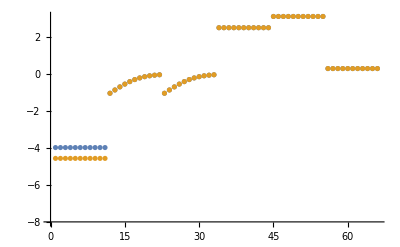

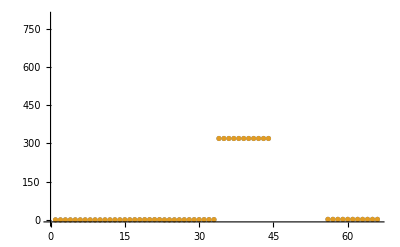

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

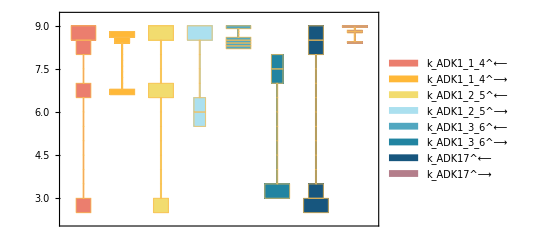

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

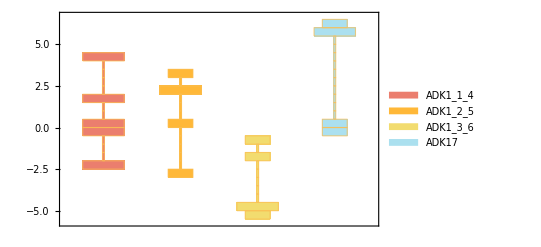

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

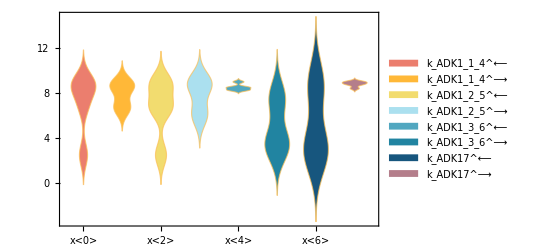

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

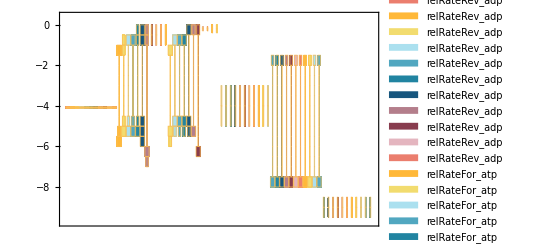

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= Underscript[E_total, Global]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
res = backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName];
{res[[1]],  Transpose@ Table[Flatten@{res[[i, 1]], res[[i, 2]][[2]], res[[i, 3]][[2]]}, {i, 2, 4}]}//TableForm
```

data value | predicted value | error in %
0.000105
0.000046
0.000044 | 0.0000272767
0.0000460006
0.0000440006 | 74.0222
0.00122562
0.00127404

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
319. | 319. | 8.04539×10^-11
1296. | 1296. | 1.12055×10^-9

```mathematica
backCalculateRatios[KeqRatio, KeqEquilibrator, paramFitSub]//TableForm
```

data value | predicted value | error in %
1.97 | 1.97 | 1.29311×10^-7